## Function

```mathematica
PlotPlate[PlateName_,sample_]:=Module[
{width=127.8, length=85.5, xA1=14.4, yA1=11.2, d=9, well, x, y, error},
Labeled[Graphics[
{{EdgeForm[AbsoluteThickness[2]],White,Rectangle[{0,0},{width-d/2,-length+d/2}]},
Table[Text[Style[x+1,16,Bold],{xA1+x*d,-yA1/3}],{x,0,11}],
Table[Text[Style[FromCharacterCode[65+y],20,Bold],{xA1/2.5,-yA1-y*d}],{y,0,7}],
Table[{EdgeForm[AbsoluteThickness[2]],White,Disk[{xA1+x*d,-yA1-y*d},d/2-0.4]},{x,0,11},{y,0,7}],
Table[If[sample[[i]]≠"",
well=ToCharacterCode[sample[[i]]];
error=0;
If[well[[1]]<65 || well[[1]]>72, error=1, y=well[[1]]-65];
Which[
	Length[well]<2 || Length[well]>3, error=1,
	Length[well]==2, If[well[[2]]<49 || well[[2]]>57, error=1, x=well[[2]]-49],
	Length[well]==3, If[well[[2]]!=49 || well[[3]]<48 || well[[3]]>50, error=1, x=10+well[[3]]-49]
];
If[error==1,
Print[sample[[i]]<>" is an incorrect well position"],
{EdgeForm[AbsoluteThickness[2]],Gray,Disk[{xA1+x*d,-yA1-y*d},d/2-0.4]}]],
{i,1,Length[sample]}]
},ImageSize->440],
TextCell[PlateName],Top,LabelStyle->Directive[FontSize->18,FontFamily->"Calibri"]]
];
```

```mathematica
SampleFromSheet[sheet_]:=Table[sheet[[i,1]],{i,2,Length[sheet]}];
```

```mathematica
ExportToPDF[plates_,filename_]:=Module[
{PlatesPerPage, ListOfPages},
PlatesPerPage=Partition[plates,UpTo[4]];
ListOfPages=Table[
Rotate[Grid[Partition[PlatesPerPage[[i]],UpTo[2]],Spacings->{0,2}],90 Degree],
{i,1,Length[PlatesPerPage]}];
Export[filename<>".pdf",CreateDocument[Riffle[ListOfPages,Cell["","PageBreak",PageBreakBelow->True]],Visible->False]]
];
```

```mathematica
FindStrandsInSheet[protocol_,sheet_]:=Module[
{StrandList,start,end,RegularStaple={},PatternStaple={},well,name,sample={}},

StrandList=StringSplit[protocol,"\n"];
start=Position[StrandList,"Internal_Tile_11"][[1,1]]+1;
end=Position[StrandList,"Create Tiles"][[1,1]]-2;
For[i=start,i≤end,i++,
If[StringMatchQ[StrandList[[i]],"   Reg"~~__],
AppendTo[RegularStaple,StringTake[StrandList[[i]],{4,14}]],
AppendTo[PatternStaple,StringTake[StrandList[[i]],{4,19}]]
]];

For[i=2,i<=Length[sheet],i++,
name=sheet[[i,2]];
well[name]=sheet[[i,1]]];
For[i=1,i<=Length[RegularStaple],i++,
If[StringQ[well[RegularStaple[[i]]]],AppendTo[sample,well[RegularStaple[[i]]]]]];
For[i=1,i<=Length[PatternStaple],i++,
If[StringQ[well[PatternStaple[[i]]]],AppendTo[sample,well[PatternStaple[[i]]]]]];
sample];
```

## Plot plate diagrams

Use PlotPlate to generate a plate diagram for your sample:
plate=PlotPlate[sample, plate name]
sample is a list of well positions, for example {“A1”,”B2”,”C3”}.

### A simple example

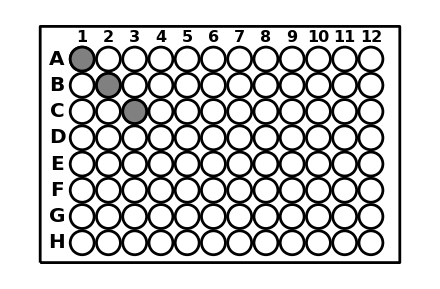
-Graphics-plate name

```mathematica
plate=PlotPlate["plate name",{"A1","B2","C3"}]
```

### A practice plate

```mathematica
sample=Flatten[{
Table["A"<>ToString[x],{x,{4,9}}],
Table["B"<>ToString[x],{x,{3,4,9,10}}],
Table["C"<>ToString[x],{x,2,11}],
Table["D"<>ToString[x],{x,1,12}],
Table["E"<>ToString[x],{x,1,12}],
Table["F"<>ToString[x],{x,2,11}],
Table["G"<>ToString[x],{x,{3,4,9,10}}],
Table["H"<>ToString[x],{x,{4,9}}]
},1];
```

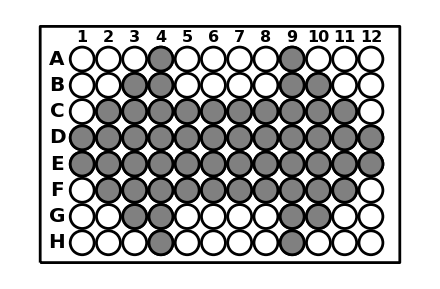
-Graphics-Practice plate: arrow

```mathematica
plate=PlotPlate["Practice plate: arrow",sample]
```

### Stock plates

Use SampleFromSheet to extract the well positions from a spreadsheet:
sample=SampleFromSheet[sheet]
sheet is imported from an excel file.

```mathematica
SetDirectory[NotebookDirectory[]];
SampleSheet=Import["origami_square.xlsx"];
SheetName=Import["origami_square.xlsx","Sheets"];
```

```mathematica
samplelist=Table[{SheetName[[i]],SampleFromSheet[SampleSheet[[i]]]},{i,Length[SampleSheet]}];
```

```mathematica
plates=Table[PlotPlate[samplelist[[i,1]],samplelist[[i,2]]],{i,Length[samplelist]}];
```

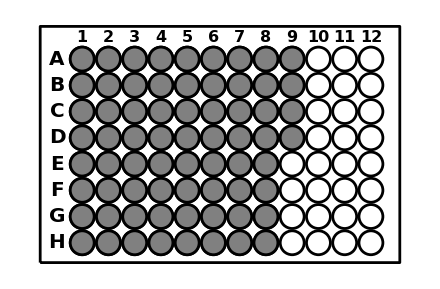
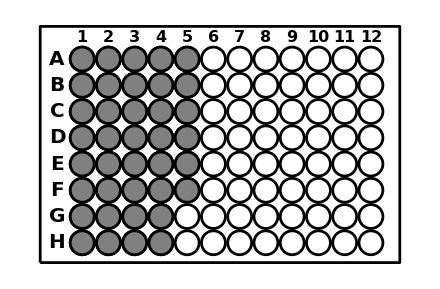
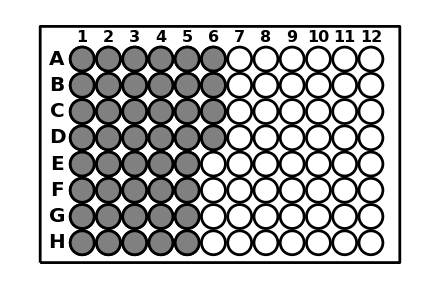
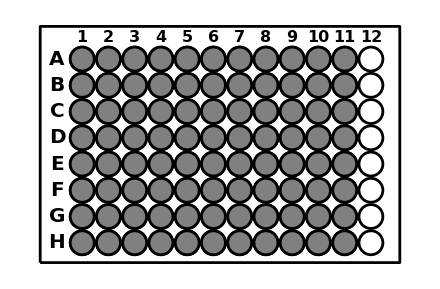
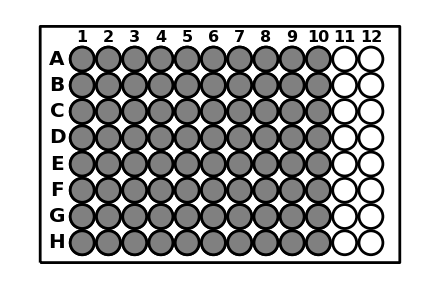
-Graphics-plate1 interior (triangle1&2) | -Graphics-plate2 interior (triangle3&4)
-Graphics-plate3 bridge | -Graphics-plate4 edge (inert)
-Graphics-plate5 pattern (triangle1&2) | -Graphics-plate6 pattern (triangle3&4)
-Graphics-plate7 edge (1nt in 5x5) | -Graphics-plate 8 edge (2nt in 5x5)

```mathematica
Grid[Partition[plates,UpTo[2]]]
```

### Find your staples in the stock plates for creating a tile with a pattern

Use FindStrandsInSheet to find the well positions of your strands:
FindStrandsInSheet[protocol, sheet]
protocol is imported from a .txt file generated by the FracTile Compiler.
sheet is imported from an excel file (“origami_square.xlsx”) with information of the stock plates.

```mathematica
SetDirectory[NotebookDirectory[]];
SampleSheet=Import["origami_square.xlsx"];
SheetName=Import["origami_square.xlsx","Sheets"];
```

Import your protocol:

```mathematica
protocol=Import["Tile2_Protocol.txt"];
```

Find the staples listed in your protocol in a stock plate:

```mathematica
sample1=FindStrandsInSheet[protocol,SampleSheet[[1]]]
```

{A1,C1,F1,G1,B2,C2,D2,G2,H2,A3,B3,C3,D3,G3,H3,A4,F4,B5,C5,D5,E5,F5,G5,A6,B6,C6,E6,G6,H6,A7,C7,E7,F7,H7,B8,C8,E8,F8,G8,H8,A9,B9,C9,D9}

Number of staples in found in this stock plate:

```mathematica
Length[sample1]
```

44

Rename the plate according to your tile name and display the plate diagram:

```mathematica
tilename="Tile2";
```

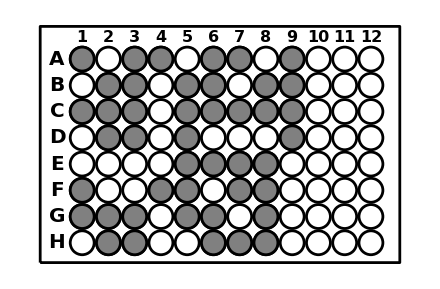
-Graphics-Tile2: plate1 interior (triangle1&2)

```mathematica
plate1=PlotPlate[tilename<>": "<>SheetName[[1]],sample1]
```

Continue to find the staples listed in your protocol in every relevant stock plate:

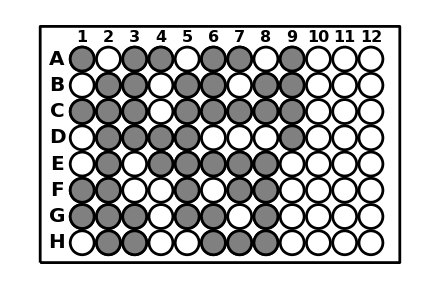
-Graphics-Tile2: plate2 interior (triangle3&4)

```mathematica
sample2=FindStrandsInSheet[protocol,SampleSheet[[2]]];
plate2=PlotPlate[tilename<>": "<>SheetName[[2]],sample2]
```

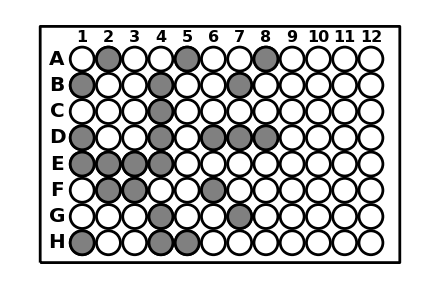
-Graphics-Tile2: plate5 pattern (triangle1&2)

```mathematica
sample3=FindStrandsInSheet[protocol,SampleSheet[[5]]];
plate3=PlotPlate[tilename<>": "<>SheetName[[5]],sample3]
```

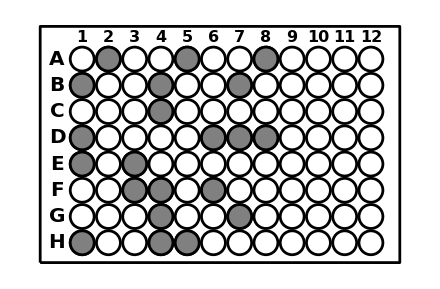
-Graphics-Tile2: plate6 pattern (triangle3&4)

```mathematica
sample4=FindStrandsInSheet[protocol,SampleSheet[[6]]];
plate4=PlotPlate[tilename<>": "<>SheetName[[6]],sample4]
```

Save the plate diagrams as a PDF file.

```mathematica
ExportToPDF[{plate1,plate2,plate3,plate4},tilename<>"_plates"];
```